# VYA - Přednášky

## 12. Přednáška

### Interpolace

Věříme hodnotám a hledáme mezi nimi

```mathematica
Quiet[Remove["Global`*"]];
```

{{0.,0.},{0.785398,0.707107},{1.5708,1.},{2.35619,0.707107},{3.14159,1.22465×10^-16},{3.92699,-0.707107},{4.71239,-1.},{5.49779,-0.707107},{6.28319,-2.44929×10^-16}}

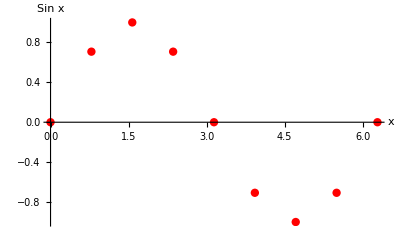

```mathematica
Data = Table[{x, Sin[x]}, {x, 0., 2 Pi, Pi/4}]
PltData = ListPlot[Data, AxesLabel->{"x", "Sin x"}, PlotStyle-> {Red, PointSize[0.015]}, GridLines->Full]
```

```mathematica
?Interpolation
Options[Interpolation]
```

{InterpolationOrder→3,Method→Automatic,PeriodicInterpolation→False}

InterpolatingFunction[…]

{0.,6.28319}

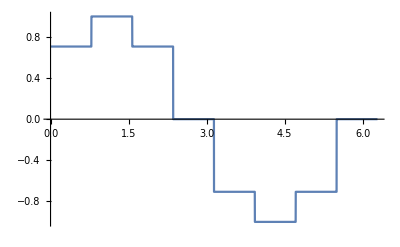

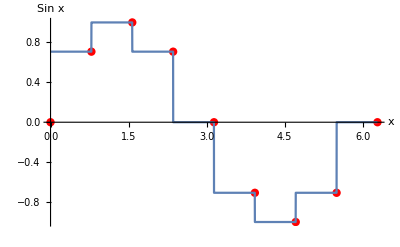

```mathematica
IntSin = Interpolation[Data, InterpolationOrder->0]
{xMin, xMax} = IntSin[[1,1]]
PltInt = Plot[IntSin[x], {x, xMin, xMax}]
Show[PltData, PltInt]
```

```mathematica
?InterpolationOrder
```

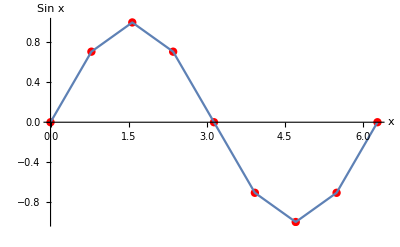

```mathematica
IntSin = Interpolation[Data, InterpolationOrder->1];
PltInt = Plot[IntSin[x], {x, xMin, xMax}];
Show[PltData, PltInt]
```

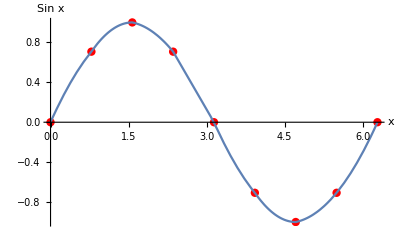

```mathematica
IntSin = Interpolation[Data, InterpolationOrder->2];
PltInt = Plot[IntSin[x], {x, xMin, xMax}];
Show[PltData, PltInt]
```

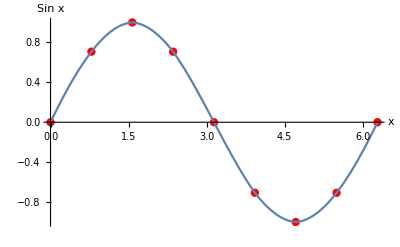

```mathematica
IntSin = Interpolation[Data, InterpolationOrder->3];
PltInt = Plot[IntSin[x], {x, xMin, xMax}];
Show[PltData, PltInt]
```

```mathematica
?InterpolationOrder
```